```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
g1=Plot[{PDF[TransformedDistribution[LogisticSigmoid[u],u\[Distributed]NormalDistribution[0,1/3]],x],PDF[TransformedDistribution[LogisticSigmoid[u],u\[Distributed]NormalDistribution[0,1]],x],PDF[TransformedDistribution[LogisticSigmoid[u],u\[Distributed]NormalDistribution[0,3]],x]},{x,0,1},Frame->{True,True,False,False},FrameLabel->{"θ","pdf"},FrameTicks->{True,None},BaseStyle->Medium,PlotStyle->{Blue,Orange,Green},PlotRange->Full]
```

```mathematica
g2=Plot[{PDF[TransformedDistribution[LogisticSigmoid[u],u\[Distributed]NormalDistribution[1,1/3]],x],PDF[TransformedDistribution[LogisticSigmoid[u],u\[Distributed]NormalDistribution[1,1]],x],PDF[TransformedDistribution[LogisticSigmoid[u],u\[Distributed]NormalDistribution[1,3]],x]},{x,0,1},Frame->{True,True,False,False},FrameLabel->{"θ","pdf"},FrameTicks->{True,None},BaseStyle->Medium,PlotStyle->{Blue,Orange,Green},PlotRange->Full]
```

```mathematica
Table[PDF[TransformedDistribution[LogisticSigmoid[u],u\[Distributed]NormalDistribution[0,3]],x],{x,0,0.1,0.02}]
```

{0.,2.92477,1.97592,1.54825,1.29715,1.12996}

## These are MUCH quicker! As per http://www.math.canterbury.ac.nz/research/ucdms2003n7.pdf

```mathematica
logitNormalPDF[μ_,σ_,p_]:=(ⅇ^(-(-μ+Log[p/(1-p)])^2/(2 σ^2)))/(√(2 π) σ p(1-p))
```

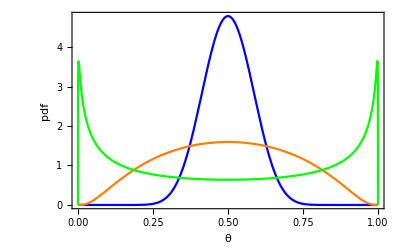

```mathematica
g1=Plot[{logitNormalPDF[0,1/3,p],logitNormalPDF[0,1,p],logitNormalPDF[0,2.5,p]},{p,0,1},Frame->{True,True,False,False},FrameLabel->{"θ","pdf"},FrameTicks->{True,True},BaseStyle->Medium,PlotStyle->{Blue,Orange,Green},PlotRange->Full]
```

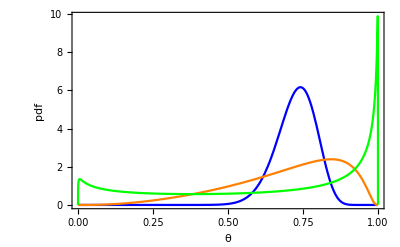

```mathematica
g2=Plot[{logitNormalPDF[1,1/3,p],logitNormalPDF[1,1,p],logitNormalPDF[1,2.5,p]},{p,0,1},Frame->{True,True,False,False},FrameLabel->{"θ","pdf"},FrameTicks->{True,True},BaseStyle->Medium,PlotStyle->{Blue,Orange,Green},PlotRange->Full]
```

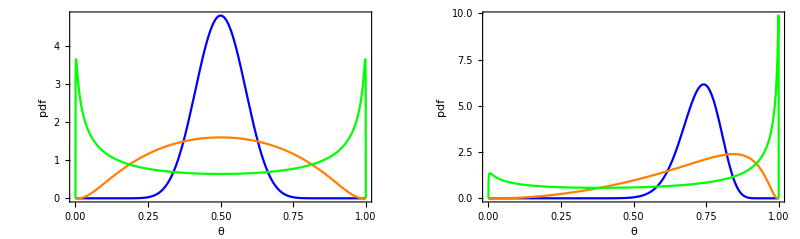

```mathematica
gFinal=Show[GraphicsRow[{g1,g2}],ImageSize->800]
```

```mathematica
Export["Distributions_logitNormal.pdf",gFinal]
```

Distributions_logitNormal.pdf

```mathematica
(ⅇ^(-(-μ+Log[p/(1-p)])^2/(2 σ^2)))/(√(2 π) σ p(1-p))/.{p->θ}
```

```mathematica
1/(√(2 π) (1-θ) θ σ)
```

```mathematica
1/(√(2 π) (1-θ) θ σ)//TeXForm
```

\frac{1}{\sqrt{2 \pi } (1-\theta ) \theta  \sigma }

```mathematica
ⅇ^(-(-μ+Log[p/(1-p)])^2/(2 σ^2))//TeXForm
```

e^{-\frac{\left(\log \left(\frac{p}{1-p}\right)-\mu \right)^2}{2 \sigma ^2}}